## Shear Analysis

L: | 80.25
m: | 1000
kappa: | 0.1
sigma: | 0.001
kappa_sigma_r: | 100.
Delta: | 0.040105
Extension Minimum: | 0
Extension Maximum: | 100
beta: | 4.
mu: | 2.32
c: | 2.45
delta: | 11.22
b: | 1.56
k: | 1.03
ev0: | 1.06
C0: | 0.47
e0: | 0.01875
beta: | 38.6817

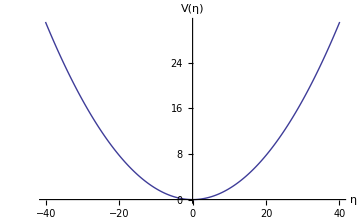

0.01875

Backbone spring constant κ:

0.1

Residue-pair spring constant σ(ϵ = 0.01875):

0.001

κ/σ ratio:

100.

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]
<<Units`
<<PhysicalConstants`

PotentialData = Import["potential_data.out","Table"];

PartitionFunction=Import["PartitionFunction_0_0.out","Table"];
FreeEnergy=Import["FreeEnergy_0_0.out","Table"];
dPartitionFunction=Import["dPartitionFunction_0_0.out","Table"];
dFreeEnergy=Import["dFreeEnergy_0_0.out","Table"];

Subscript[R, pfmxd]=Import["pfmxd_r.out","Table"];
Subscript[R, mxd]=Import["mxd_r.out","Table"];

Subscript[λ, pfmxd]=Import["pfmxd_lambda.out","Table"];
Subscript[λ, mxd]=Import["mxd_lambda.out","Table"];

Subscript[ρ, pfmxd]=Import["pfmxd_roe.out","Table"];
Subscript[ρ, mxd]=Import["mxd_roe.out","Table"];

Parameters=Import["Parameters"];
Grid[Parameters]
Needs["PlotLegends`"]
PlotPotentialData=ListLinePlot[{PotentialData},ImageSize->Medium,AxesOrigin->{0,0},AxesLabel->{Style["η",FontSize->18],Style["V(η)",FontSize->18]},PlotStyle->Thick,PlotRange->All]

ϵ=Parameters[[17,2]]
β=Parameters[[18,2]];

L=Parameters[[1,2]];
m=Parameters[[2,2]];
Δ=Parameters[[6,2]];
Print["Backbone spring constant κ:"]
κ=Parameters[[3,2]]
Print["Residue-pair spring constant σ(ϵ = "<>ToString[ϵ]<>"):"]
σ=Parameters[[4,2]]
Print["κ/σ ratio:"]
κσr=Parameters[[5,2]]
umax=Parameters[[7,2]];
umax=Parameters[[8,2]];

n=ToExpression[StringTrim[Last[StringSplit[Directory[],"/"]],RegularExpression["N*"]]];

fsTitle=24;
fsAxesLabel=18;
fs2=16;

Subscript[η, B]=0.5;

ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)
ToForceDimension[f_]:=(f (κ/(2β))^(1/2)) ToNewton;
ToDimension[η_]:=η ((κ β)/2)^(-1/2)(*Converts to Å*)
```

### Length Dimension Check

```mathematica
Subscript[η, B] (*No Dimension*)
ToDimension[Subscript[η, B]](*Å*)
```

0.5

0.359528

### Force Dimension Check

```mathematica
0.5 (*No Dimension*)
σ ToDimension[Subscript[η, B]] ToNewton  (*pN*)
ToForceDimension[0.5] (*Converts force to dimensions of eV/Å then to J/m for pN*)
```

0.5

0.576027

28.8013

Partition function & Free Energy

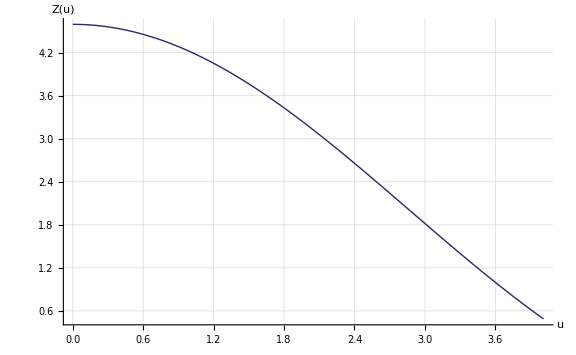
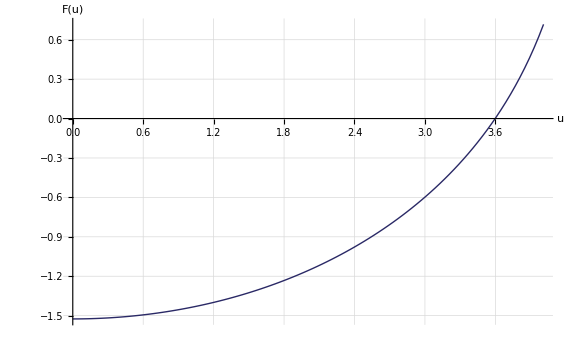

```mathematica
pIntactPF=ListLinePlot[PartitionFunction,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["Z(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

pIntactFE=ListLinePlot[FreeEnergy,ImageSize->Large,PlotStyle->{Thick,Darker[ColorData[1,1]]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}];

{pIntactPF,pIntactFE}
```

Residue-pair separations (x-z), (x-y), (z-y)

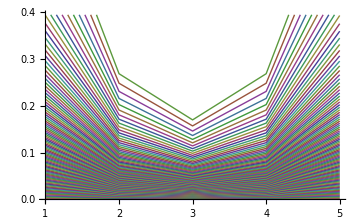
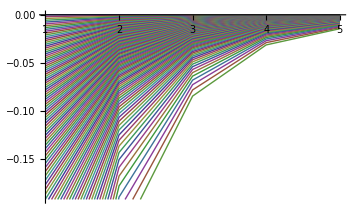

0.511366

0 | 0 | 0 | 0 | 0
0.00193767 | 0.000766595 | 0.000485117 | 0.000766595 | 0.00193767
0.00387594 | 0.00153343 | 0.000970386 | 0.00153343 | 0.00387594
0.00581543 | 0.00230074 | 0.00145596 | 0.00230074 | 0.00581543
0.00775674 | 0.00306878 | 0.00194199 | 0.00306878 | 0.00775673
0.00970047 | 0.00383777 | 0.00242862 | 0.00383777 | 0.00970047
0.0116473 | 0.00460798 | 0.00291602 | 0.00460798 | 0.0116473
0.0135977 | 0.00537963 | 0.00340434 | 0.00537963 | 0.0135977
0.0155525 | 0.00615298 | 0.00389373 | 0.00615298 | 0.0155525
0.0175121 | 0.00692828 | 0.00438436 | 0.00692828 | 0.0175121
0.0194773 | 0.00770577 | 0.00487638 | 0.00770577 | 0.0194773
0.0214488 | 0.00848573 | 0.00536995 | 0.00848573 | 0.0214488
0.0234271 | 0.0092684 | 0.00586524 | 0.0092684 | 0.0234271
0.0254129 | 0.0100541 | 0.00636242 | 0.0100541 | 0.0254129
0.027407 | 0.010843 | 0.00686165 | 0.010843 | 0.027407
0.0294099 | 0.0116354 | 0.00736311 | 0.0116354 | 0.0294099
0.0314225 | 0.0124316 | 0.00786699 | 0.0124316 | 0.0314225
0.0334454 | 0.0132319 | 0.00837344 | 0.0132319 | 0.0334454
0.0354794 | 0.0140366 | 0.00888267 | 0.0140366 | 0.0354794
0.0375252 | 0.014846 | 0.00939487 | 0.014846 | 0.0375252
0.0395836 | 0.0156604 | 0.00991022 | 0.0156604 | 0.0395836
0.0416555 | 0.0164801 | 0.0104289 | 0.0164801 | 0.0416555
0.0437415 | 0.0173054 | 0.0109512 | 0.0173053 | 0.0437415
0.0458427 | 0.0181366 | 0.0114772 | 0.0181366 | 0.0458427
0.0479597 | 0.0189742 | 0.0120073 | 0.0189742 | 0.0479597
0.0500937 | 0.0198184 | 0.0125415 | 0.0198184 | 0.0500937
0.0522454 | 0.0206697 | 0.0130802 | 0.0206697 | 0.0522454
0.0544158 | 0.0215284 | 0.0136236 | 0.0215284 | 0.0544158
0.0566059 | 0.0223949 | 0.0141719 | 0.0223949 | 0.0566059
0.0588168 | 0.0232696 | 0.0147255 | 0.0232696 | 0.0588168
0.0610496 | 0.0241529 | 0.0152845 | 0.0241529 | 0.0610496
0.0633053 | 0.0250453 | 0.0158492 | 0.0250453 | 0.0633053
0.0655851 | 0.0259473 | 0.01642 | 0.0259473 | 0.0655851
0.0678902 | 0.0268593 | 0.0169971 | 0.0268593 | 0.0678902
0.0702219 | 0.0277817 | 0.0175809 | 0.0277817 | 0.0702219
0.0725815 | 0.0287153 | 0.0181716 | 0.0287153 | 0.0725815
0.0749704 | 0.0296604 | 0.0187697 | 0.0296604 | 0.0749704
0.07739 | 0.0306176 | 0.0193755 | 0.0306176 | 0.07739
0.0798418 | 0.0315876 | 0.0199893 | 0.0315876 | 0.0798418
0.0823274 | 0.032571 | 0.0206116 | 0.032571 | 0.0823274
0.0848484 | 0.0335684 | 0.0212428 | 0.0335684 | 0.0848484
0.0874066 | 0.0345805 | 0.0218832 | 0.0345805 | 0.0874066
0.0900038 | 0.035608 | 0.0225335 | 0.035608 | 0.0900038
0.092642 | 0.0366517 | 0.023194 | 0.0366517 | 0.092642
0.0953232 | 0.0377125 | 0.0238653 | 0.0377125 | 0.0953232
0.0980495 | 0.0387911 | 0.0245478 | 0.0387911 | 0.0980495
0.100823 | 0.0398885 | 0.0252423 | 0.0398885 | 0.100823
0.103647 | 0.0410055 | 0.0259492 | 0.0410055 | 0.103647
0.106523 | 0.0421433 | 0.0266692 | 0.0421433 | 0.106523
0.109454 | 0.0433028 | 0.0274029 | 0.0433028 | 0.109454
0.112442 | 0.0444853 | 0.0281512 | 0.0444853 | 0.112442
0.115492 | 0.0456918 | 0.0289148 | 0.0456918 | 0.115492
0.118606 | 0.0469238 | 0.0296944 | 0.0469238 | 0.118606
0.121787 | 0.0481825 | 0.0304909 | 0.0481825 | 0.121787
0.12504 | 0.0494694 | 0.0313052 | 0.0494694 | 0.12504
0.128368 | 0.050786 | 0.0321385 | 0.050786 | 0.128368
0.131776 | 0.0521341 | 0.0329915 | 0.0521341 | 0.131776
0.135267 | 0.0535153 | 0.0338656 | 0.0535153 | 0.135267
0.138847 | 0.0549317 | 0.0347619 | 0.0549317 | 0.138847
0.142521 | 0.0563852 | 0.0356817 | 0.0563852 | 0.142521
0.146294 | 0.057878 | 0.0366264 | 0.057878 | 0.146294
0.150173 | 0.0594126 | 0.0375976 | 0.0594126 | 0.150173
0.154164 | 0.0609915 | 0.0385967 | 0.0609915 | 0.154164
0.158274 | 0.0626175 | 0.0396256 | 0.0626174 | 0.158274
0.16251 | 0.0642935 | 0.0406863 | 0.0642935 | 0.16251
0.166881 | 0.0660228 | 0.0417806 | 0.0660228 | 0.166881
0.171396 | 0.0678089 | 0.0429109 | 0.0678089 | 0.171396
0.176064 | 0.0696558 | 0.0440796 | 0.0696558 | 0.176064
0.180896 | 0.0715675 | 0.0452894 | 0.0715675 | 0.180896
0.185904 | 0.0735488 | 0.0465432 | 0.0735488 | 0.185904
0.1911 | 0.0756045 | 0.0478441 | 0.0756045 | 0.1911
0.196499 | 0.0777402 | 0.0491957 | 0.0777402 | 0.196499
0.202115 | 0.0799621 | 0.0506017 | 0.0799621 | 0.202115
0.207965 | 0.0822767 | 0.0520664 | 0.0822767 | 0.207965
0.214069 | 0.0846916 | 0.0535946 | 0.0846916 | 0.214069
0.220447 | 0.0872148 | 0.0551914 | 0.0872148 | 0.220447
0.227122 | 0.0898556 | 0.0568626 | 0.0898556 | 0.227122
0.23412 | 0.0926242 | 0.0586146 | 0.0926242 | 0.23412
0.241469 | 0.095532 | 0.0604546 | 0.095532 | 0.241469
0.249203 | 0.0985916 | 0.0623909 | 0.0985917 | 0.249203
0.257358 | 0.101818 | 0.0644324 | 0.101818 | 0.257358
0.265974 | 0.105227 | 0.0665896 | 0.105227 | 0.265974
0.275099 | 0.108837 | 0.0688741 | 0.108837 | 0.275099
0.284786 | 0.112669 | 0.0712994 | 0.112669 | 0.284786
0.295096 | 0.116748 | 0.0738808 | 0.116748 | 0.295096
0.306101 | 0.121102 | 0.0766358 | 0.121102 | 0.306101
0.31788 | 0.125762 | 0.079585 | 0.125762 | 0.31788
0.33053 | 0.130767 | 0.082752 | 0.130767 | 0.33053
0.344161 | 0.13616 | 0.0861647 | 0.13616 | 0.344161
0.358904 | 0.141992 | 0.0898558 | 0.141992 | 0.358904
0.374915 | 0.148327 | 0.0938642 | 0.148327 | 0.374915
0.392378 | 0.155236 | 0.0982364 | 0.155236 | 0.392378
0.411519 | 0.162808 | 0.103028 | 0.162808 | 0.411519
0.432609 | 0.171152 | 0.108309 | 0.171152 | 0.432609
0.455984 | 0.1804 | 0.114161 | 0.1804 | 0.455984
0.482062 | 0.190717 | 0.12069 | 0.190717 | 0.482061
0.511366 | 0.20231 | 0.128026 | 0.20231 | 0.511366
0.544568 | 0.215446 | 0.136339 | 0.215446 | 0.544568
0.582541 | 0.230469 | 0.145846 | 0.230469 | 0.582541
0.626437 | 0.247836 | 0.156836 | 0.247836 | 0.626437
0.677812 | 0.268161 | 0.169698 | 0.268161 | 0.677813

Extension U (End base-pair separations at η_B) = 96

Extension U in terms of η = 3.85008 (96Δ)

```mathematica
xzpair=-(√3 Subscript[λ, mxd]+Subscript[ρ, mxd])/(√2);
xypair=√2 Subscript[ρ, mxd];

{ListLinePlot[xzpair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}],ListLinePlot[xypair,PlotStyle->Thick,ImageSize->Medium,AxesOrigin->{1,0}]}
NearestValue=Nearest[Transpose[Chop[xzpair,10^-5]][[1]],Subscript[η, B]][[1]]
upos=Flatten[Position[Transpose[Chop[xzpair,10^-5]][[1]],NearestValue]][[1]];
U=upos-1;
Grid[Chop[xzpair,10^-5],Background->{Automatic,{upos->Yellow}}]
Print["Extension U (End base-pair separations at \!\(\*SubscriptBox[\"η\", \"B\"]\)) = ",U]
Print["Extension U in terms of η = ",U Δ," (",U,"Δ)"]
```

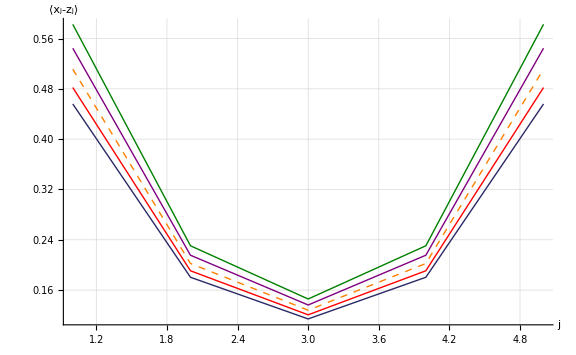
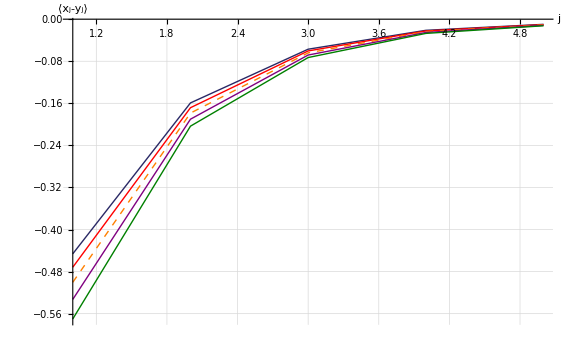

```mathematica
pos1=upos-2;
pos2=upos-1;
pos3=upos;
pos4=upos+1;
pos5=upos+2;

pxzpair=ListLinePlot[{xzpair[[pos1]],xzpair[[pos2]],xzpair[[pos3]],xzpair[[pos4]],xzpair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-z_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

pxypair=ListLinePlot[{xypair[[pos1]],xypair[[pos2]],xypair[[pos3]],xypair[[pos4]],xypair[[pos5]]},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red},{Thick,Dashed,Orange},{Thick,Purple},{Thick,Darker[Green,0.5]}},PlotLegend->{Style["u="<>ToString[(pos1-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos2-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos3-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos4-1) Δ],FontSize->fs2],Style["u="<>ToString[(pos5-1) Δ],FontSize->fs2]},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],PlotRange->All,AxesOrigin->{1,0},AxesLabel->{Style["j",FontSize->fsAxesLabel],Style["⟨x_j-y_j⟩",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->0.55,LegendPosition->{0.9,-.2}];

{pxzpair,pxypair}
```

### Force-Extension

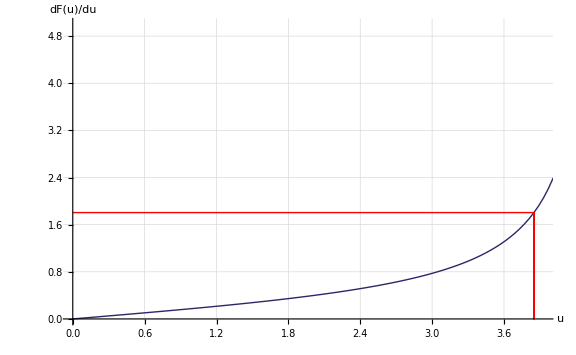

Dimensionless force at (U = 96Δ) = 1.80494

Dimensional Force = 103.969 pN
Dimensional Extension = 2.76842 Å

```mathematica
fpos={{0,dFreeEnergy[[upos]][[2]]},{dFreeEnergy[[upos]][[1]],dFreeEnergy[[upos]][[2]]},{dFreeEnergy[[upos]][[1]],0},{dFreeEnergy[[upos]][[1]],dFreeEnergy[[upos]][[2]]}};
F=dFreeEnergy[[upos]][[2]];
u=dFreeEnergy[[upos]][[1]];

p=ListLinePlot[{dFreeEnergy,fpos},ImageSize->Large,PlotStyle->{{Thick,Darker[ColorData[1,1]]},{Thick,Red}},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->{{0,Δ(upos+1)},{0,5}},AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF(u)/du",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}]

Print["Dimensionless force at (U = ",U,"Δ) = ",F]

Fc=ToForceDimension[F];
Print["\nDimensional Force = ",Fc pN,"\nDimensional Extension = ",ToDimension[u] Å,"\n"]
Export["N"<>ToString[n]<>"_sim.data",{{n,Fc,NearestValue,κσr}},"Table"];
```